## Error Bars

How to  Add Error Bars to Charts and Plots

Plots of data based on measurements often have vertical lines or intervals centered at the points to indicate the associated error estimates. Mathematica lets you add such error bars to charts and plots in two different ways.

The following steps calculate and then plot the mean high temperatures in St. Louis for each month in 2009.

Use WeatherDatapaclet:ref/WeatherData to import the daily high temperatures in St. Louis from 2009 (the large output is suppressed with ";" at the end of the command):

```mathematica
rawData=WeatherData["Saint Louis","MaxTemperature",{{2009,1,1},{2009,12,31},"Day"}];
```

Use GatherBypaclet:ref/GatherBy to group the data by month:

```mathematica
rawDataByMonth=GatherBy[rawData,#[[1,2]]&];
```

Get only the data points for each month:

```mathematica
filteredDataByMonth=Table[Last/@rawDataByMonth[[i]],{i,1,12}]
```

{{6,8.89,14.39,14,-1,0,4,3,14,9.39,5.61,6,6,5.61,-8.28,-10,8,4.39,2,-2,7.22,14.39,8.28,1,-7.78,-6,-6.72,-3,3,2,12.22},{9.39,5,1.72,-3.89,5,16.72,20,17.22,21,20,16.11,14,9.39,6,4,4,5,12,2,7.78,8,2,3,8.89,21,19,19,1},{1,0.61,2,15.61,19.39,28.89,25,23,14,26.11,17,2,9.39,14.39,16.72,21,25,22.22,15.61,14.39,15,21.72,23.28,21.11,16.11,17,15,11,9.39,18,17},{19,16.72,14.39,18.28,18.89,7.78,11.11,16.11,14.39,11,15,12.78,12,10,17.22,17,23.28,21.72,17,17.78,16,23.89,26.11,30.61,29.39,29.39,24,19,23,21},{18,18.28,18,22,23,20.61,27,25.61,21.72,19.39,22,23,28,25,29.39,27.22,18.89,21.11,26.11,27.22,29.39,31.11,28.89,28.28,26.11,27.22,29.39,20,26.72,30,27},{32.78,31,23,22.78,26.72,27,27.78,28,25,31.11,29,23.28,31.72,27,26,28.89,34,34.39,35,33.28,36.11,35,37.22,35,35,35.61,36.11,33,33.28,32},{28,29,31.11,27.22,25,29.39,31,31.11,33.28,30.61,31.11,30,29,27.78,29.39,30.61,26,25,26.72,29,25,26,29.39,32,30.61,30,31.11,33.89,29.39,28.28,29},{26.72,28.28,33.28,31.72,32.22,30.61,32,35,35,31.72,31.11,30,30,31.11,32.78,33.89,32,28.28,33,28.89,26,24.39,25.61,26.11,28,31,31,26,26,22.78,22.22},{24,24,27.78,27.22,23,25,27.78,27.78,28.28,28.28,28,27.78,26.11,27.22,26.11,29,26.72,27.22,27,21,27.78,27,26.11,23,25,21,27.22,23,19,21.11},{22,21,16,18.89,21.72,20.61,18.28,14,13,14.39,13,14.39,12.22,9,9,8,11.11,14,22,23.89,18.28,16,17,16.11,19.39,16,12,14.39,16,21.11,13.28},{16.11,20.61,16.11,18,15.61,21.11,24,24,20,16.11,17,14,17.22,21.11,16.11,11,11,8.28,11,15,17.22,16,14,12,11,6.11,12.22,21.11,15,8},{13.28,7.78,3.28,0.61,3.89,3.28,4,4,7.22,-3,4.39,3.28,7,12,4.39,2,11.11,7.22,3,-1,2,4,10,10,11,-0.61,-1,4,-1,1,2.22}}

Calculate the mean for each month:

```mathematica
meanData=Mean/@filteredDataByMonth
```

{3.6971,9.7975,16.0626,18.4613,24.6987,30.8687,29.1935,29.5716,25.65,16.0019,15.5347,4.49484}

Define a function that calculates the standard error of a dataset. Here, the standard error is the standard deviation divided by the square root of the number of observations in the dataset:

```mathematica
standardError[data_]:=StandardDeviation[data]/Sqrt[Length[data]]
```

Calculate the standard error of the high temperatures for each month:

```mathematica
stdErrorData=standardError/@filteredDataByMonth
```

{1.24482,1.38533,1.3326,1.07331,0.725073,0.79187,0.414308,0.621351,0.484215,0.75346,0.835263,0.76051}

Next, define a function that will let you put error bars on a bar chart:

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
```

This function takes its data points as data->error. Here, the means and associated standard errors are put into this form:

```mathematica
chartData=Table[meanData[[i]]->stdErrorData[[i]],{i,1,Length[meanData]}]
```

{3.6971→1.24482,9.7975→1.38533,16.0626→1.3326,18.4613→1.07331,24.6987→0.725073,30.8687→0.79187,29.1935→0.414308,29.5716→0.621351,25.65→0.484215,16.0019→0.75346,15.5347→0.835263,4.49484→0.76051}

Before making the chart, create and style labels for each month:

```mathematica
labels={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sept","Oct","Nov","Dec"};
```

Use BarChartpaclet:ref/BarChart to make the chart:

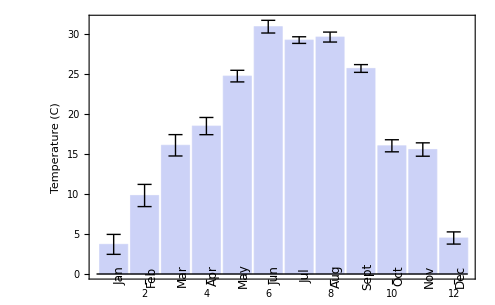

```mathematica
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[labels,Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],Frame->Left,FrameLabel->{None,Style["Temperature (C)",12,FontFamily->"Arial"]}]
```

You can also show this data and associated errors in a plot where each mean is joined by a line.

To do this, first load the ErrorBar Plotting Package:

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorListPlotpaclet:ErrorBarPlots/ref/ErrorListPlot, which is part of this package, takes its data in a list as {data,error}. Here, the data is put into this form:

```mathematica
plotData=Partition[Riffle[meanData,stdErrorData],2]
```

{{3.6971,1.24482},{9.7975,1.38533},{16.0626,1.3326},{18.4613,1.07331},{24.6987,0.725073},{30.8687,0.79187},{29.1935,0.414308},{29.5716,0.621351},{25.65,0.484215},{16.0019,0.75346},{15.5347,0.835263},{4.49484,0.76051}}

Set up tick labels to use with ErrorListPlotpaclet:ErrorBarPlots/ref/ErrorListPlot:

```mathematica
tickSpecs={{{1,"Jan"},{2,"Feb"},{3,"Mar"},{4,"Apr"},{5,"May"},{6,"Jun"},{7,"Jul"},{8,"Aug"},{9,"Sept"},{10,"Oct"},{11,"Nov"},{12,"Dec"}},Automatic};
```

Plot the data with ErrorListPlotpaclet:ErrorBarPlots/ref/ErrorListPlot:

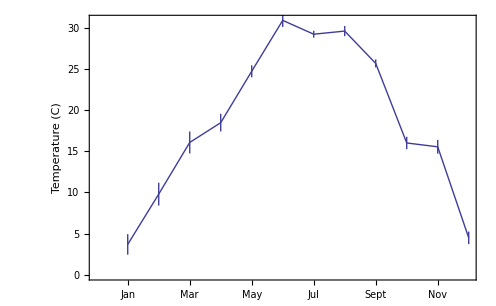

```mathematica
ErrorListPlot[plotData,Joined->True,Frame->{Left,Bottom},FrameTicks->tickSpecs,FrameLabel->{None,Style["Temperature (C)",12,FontFamily->"Arial"]}]
```

## Tutorials

The Structure of Graphicspaclet:tutorial/TheStructureOfGraphics

Options for Graphicspaclet:tutorial/Options

Plotting Lists of Datapaclet:tutorial/PlottingListsOfData

Graphics and Soundpaclet:tutorial/GraphicsAndSoundOverview

## Related Links

How to: Create Plotspaclet:howto/CreatePlots

How to: Customize Plots and Graphicspaclet:howto/CustomizePlotsAndGraphics

How to: Do Statistical Analysispaclet:howto/DoStatisticalAnalysis

## See Also

StandardDeviationpaclet:ref/StandardDeviation  ▪  Sqrtpaclet:ref/Sqrt  ▪  Lengthpaclet:ref/Length  ▪  BarChartpaclet:ref/BarChart  ▪  ErrorListPlotpaclet:ErrorBarPlots/ref/ErrorListPlot

## More About

ErrorBar Plotting Packagepaclet:ErrorBarPlots/guide/ErrorBarPlottingPackage

Data Visualizationpaclet:guide/DataVisualization

Numerical Datapaclet:guide/NumericalData

Function Visualizationpaclet:guide/FunctionVisualization

Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling